# Основы языка Wolfram

## 1 Введение

### 1.1 Первый принцип: Everything is an expression

#### 1.1.1 Атомы

Атомы: символы, числа, строки.
Числа: Integer, Real, Rational, Complex

```mathematica
{AtomQ[5],AtomQ["hello"],AtomQ[1+2*I],AtomQ[2/3],AtomQ[f[x]],AtomQ[f]}
```

#### 1.1.2 Нормальные (составные) выражения

```mathematica
expr[el1,el2,...,eln]
```

#### 1.1.3 Внутренняя (полная) форма выражений (FullForm)

```mathematica
a=z*Sin[x+y]
FullForm[%]
```

```mathematica
TreeForm[z*Sin[x^2+y]]
```

```mathematica
TreeForm[E^(Cos[y+2x]+Sin[3z])]
```

#### 1.1.5 Заголовки выражений

```mathematica
Head[a]
```

```mathematica
FullForm[Hold[aa;bb;c+d;]]
```

```mathematica
Clear[b,f,g,h,x];
b=f[g][h][x];
Head[b]
{Head[f[g][h]],Head[f[g]],Head[f]}
```

```mathematica
{Head[1],Head[2/3],Head["Hi"],Head[2*I+3]}
```

#### 1.1.6 Доступ к частям выражений через индексы

```mathematica
FullForm[a]
```

```mathematica
{a⟦0⟧,a⟦1⟧,a⟦1,0⟧,a⟦2⟧,a⟦2,0⟧,a⟦2,1⟧,a⟦2,1,0⟧,a⟦2,1,1⟧,a⟦2,1,2⟧}
```

```mathematica
a⟦2,1⟧=π
a
```

```mathematica
aaa=2/3
FullForm[aaa]
{Numerator[aaa],Denominator[aaa]}
```

#### 1.1.7 Уровни выражений, Level

```mathematica
Clear[a]
a=z*Sin[x+y]+z1 Cos[x1+y1];
FullForm[a]
TreeForm[a]
```

```mathematica
Level[a,{0}]
Level[a,{1}]
Level[a,{2}]
Level[a,{3}]
Level[a,{4}]
```

```mathematica
Level[a,{-1}]
Level[a,{-2}]
Level[a,{-3}]
Level[a,{-4}]
```

```mathematica
Level[a,{2}]
lev3=Level[a,3]//Sort
lev3j=Join[Level[a,{1}],Level[a,{2}],Level[a,{3}]]//Sort
```

### 1.2 Второй принцип: сопоставление с образцом (pattern matching) и подстановка по правилам (rule substitution)

#### 1.2.1 Правила преобразования

```mathematica
Clear[a,b,c,d,e]
```

```mathematica
FullForm[a->b]
```

```mathematica
{a,b,c,d}/.a->b
```

```mathematica
FullForm[Hold[{a,b,c,d}/.a->b]]
```

```mathematica
FullForm[x_]
```

```mathematica
{1,2,f[1,2],f[3],f["sss"]}/.f[x_]->x^2
```

#### 1.2.2 Пример простой функции

```mathematica
Clear[f];
f[x_]:=x^2
{f[2],f["word"],f[Newton]}
```

#### 1.2.3 На самом деле функции -- это правила

```mathematica
DownValues[f]
```

#### 1.2.4 Пример функции с ограниченным шаблоном

```mathematica
Clear[f]
f[x_Integer]:=x^2
{f[2],f[Pi],f[Newton]}
```

#### 1.2.5 Немного о вычислении

выражение не изменяется, если нет ни одного правила, шаблон которого подходит этому выражению

каждому введенному выражению применяются все имеющиеся в данный момент в базе правила, причем циклически (до тех пор, пока к выражению больше не подходит ни одно правило)

#### 1.2.6 Шаблоны позволяют давать различные определения для одной и той же функции

```mathematica
FullForm[x_?EvenQ]
```

```mathematica
Clear[f]
f[x_?EvenQ]:=x
f[x_?OddQ]:=x^2
f[x_]:=Sin[x]
{f[1],f[2],f[3],f[3/2],f[Leibnitz],f[Pi]}
```

#### 1.2.7 Некоммутативность применения правил

к выражению применяется первое найденное в базе правило, выражение изменяется согласно ему

остальные правила, подходящие к выражению, после этого не применяются

результат зависит от порядка, в котором записаны правила в глобальной базе правил

```mathematica
Clear[f]
f[x_?EvenQ]:=x
f[x_?OddQ]:=x^2
f[x_]:=Sin[x]
{f[1],f[2],f[3],f[4],f[3/2],f[Einstein],f[Pi]}
```

```mathematica
DownValues[f]
```

#### 1.2.8 Автоматическое упорядочивание правил

Правила преобразований упорядочиваются по убыванию “общности”, то есть самые общие правила применяются в последнюю очередь. В частности, пользовательские правила применяются раньше встроенных.

```mathematica
Clear[f]
f[x_]:=Sin[x]
f[x_?EvenQ]:=x
f[x_?OddQ]:=x^2

{f[1],f[2],f[3],f[4],f[3/2],f[Einstein],f[Pi]}
```

### 1.3. Третий принцип: вычисление выражений

```mathematica
FullForm[Sin[Pi+Pi]]
```

```mathematica
Trace[Sin[Pi+Pi]]
```

## 2 Элементарные операции

### 2.2 Символы и переменные

```mathematica
Head[foo]
```

```mathematica
Head[foo_bar]
```

```mathematica
Head[Unevaluated[a&&True]]
```

```mathematica
Information[Plot]
```

```mathematica
a[1]=x
a[2][3]=y

SubValues[a]
```

### 2.4 Присваивания

```mathematica
Clear[a,b]
FullForm[Hold[a=b]]
FullForm[Hold[a:=b]]
```

```mathematica
a=RandomReal[]
Do[Print[a],{5}]
```

```mathematica
c=3
d:=777
```

```mathematica
b:=RandomReal[]
Do[Print[b],{5}]
```

### 2.5 Проверки на равенство

```mathematica
Sin[x]^2+Cos[x]^2===1
```

```mathematica
Which
Switch
```

### 2.6 Логические операции

### 2.7 Условные переходы

### 2.8 Циклы

## 3 Списки

### Создание списков

```mathematica
Range
```

```mathematica
Table[1,{10}]
Table[i,{i,5}]
Table[i,{i,3,15,6}]
```

```mathematica
Array[f,{5}]
Array[f,{5,3}]
```

```mathematica
Append Prepend AppendTo PrependTo
```

### Части списков

```mathematica
expr=a[b[1,2],c[3,4,f[5,6]],d[k[0,1],g[9,10,11],l[2,3]],e[h[12]]]
TreeForm[expr]
```

```mathematica
expr[[1,1]]
expr[[All,1]]
expr[[All,All,0]]
```

```mathematica
Part Extract Span
```

```mathematica
FullForm[Hold[t[[2;;3]]]]
```

```mathematica
ClearAll[t,a]
t=Array[a,{5,5}]
t⟦2⟧
t⟦All,3⟧
MatrixForm[t⟦All,2;;4⟧]
MatrixForm[t⟦All,2;;5;;2⟧]
```

```mathematica
t⟦3,1⟧
```

```mathematica
Part[t,{1,2}]
Extract[t,{1,2}]
Extract[t,{{1,2},{3,2},{5,1}}]
```

```mathematica
Take Drop
```

```mathematica
testlist=Range[1,20,3]
Take[testlist,{2,4}]
Part[testlist,Span[2,4]]
```

```mathematica
Rest[Range[5]]
Most[Range[5]]
```

```mathematica
Length[t]
Dimensions[t]
```

```mathematica
t⟦All,3⟧=Range[5]
MatrixForm[t]
t⟦All,3⟧=zzz
MatrixForm[t]
```

```mathematica
ReplacePart[t⟦1⟧,q,5]
MatrixForm[t]
ReplacePart[Range[7],q,5]
```

```mathematica
t[[1,3]]=t[[3,3]]=x
MatrixForm[t]
pos=Position[t,zzz]
Position[First[t],zzz]
```

```mathematica
Extract[t,pos]
```

```mathematica
pos⟦All,1⟧
Map[Most,pos]
Extract[t,Map[Most,pos]]
```

```mathematica
fun[x_List,elem_]:=Extract[x,Map[Most,Position[x,elem]]]
fun[t,zzz]
fun[t,a[1,1]]
fun[t,x]
```

```mathematica
complextestlist1=Map[Range,Range[6]]
```

```mathematica
step1list=Position[complextestlist1,_?OddQ]
```

```mathematica
step2list=Split[step1list,First[#1]== First[#2]&]
```

```mathematica
step3list=Map[First,step2list,{2}]
```

```mathematica
step4list=Cases[step3list,x_List/;OddQ[Length[x]]]
step5list=Union[Flatten[step4list]]
complextestlist1[[step5list]]
```

```mathematica
Select решает
```

### Добавление и удаление элементов

```mathematica
Append Prepend AppendTo PrependTo
```

```mathematica
Insert Delete
```

```mathematica
Length
```

### Вложенные списки

```mathematica
Partition Transpose
```

```mathematica
Flatten
```

### Операции с несколькими списками

```mathematica
Join
```

```mathematica
Union Intersection Complement
```

### Сортировка

```mathematica
Sort Split Ordering
```

```mathematica
l={5,3,4,8,9,2,3,4,0,1,4,7};
Sort[l]
Sort[l,Greater]
Sort[{{1,2,3},{7,3,4,5,2,3,4},{4,3,2},{2},{100,20}}]
```

## 4 Правила, шаблоны

```mathematica
Clear[a,q,r,expr]
r={x_}->q[x];
expr={{{a}}}
expr/.r
expr/.r/.r/.r
expr/.List->q
```

```mathematica
Clear[x,y,z,g,h,a];
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]->f[10]}
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x,z_]->f[10,z]}
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],Cos[y]}/.{f_[x,z_]->{{"f now",f},{"z now",z}}}
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]:>f[10],f_[x,y_]:>f[10,y],f_[z_,x]->f[z,10]}
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]->f[10],f_[x,y_]->f[10,y],f_[z_,x]->f[z,10],f_[x,y_,z_]->f[10,y,z]}
```

```mathematica
expr=a[b[1],2,c[3,d[5,6],e[7]],4];
ReplaceAll[expr,f_[x__]:> {Print[f[x]];f[x]}]
Replace[expr,f_[x__]:> {Print[f[x]];f[x]},Infinity]
```

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List->{{"function",f},{"args",{t}}}
```

x | 
function
Sin | args
x
function
Power | args | 
x | 2
function
Times | args | 
x | y
function
Plus | args | 
x | y
function
g | args | 
y | x
function
h | args |  | 
x | y | z
function
Cos | args
y

## 5 Функции

```mathematica
Clear[f,x,a,b,c,d,h];
f[x_]:=x=5;
```

```mathematica
a
f[a];
a
```

a

5

```mathematica
b=c;
f[b];
```

```mathematica
Clear[c];
b
```

c

```mathematica
Clear[a];
f[2 a]
```

Set::write: Tag Times in 2\ a is Protected.

5

```mathematica
Clear[b,c];
b=c;
f[b];
```

```mathematica
f[b]
```

Set::setraw: Cannot assign to raw object 5.

5

```mathematica
ClearAll[ff,a];
SetAttributes[ff,HoldFirst];
f[x_]:=x=5;
ff[x_]:=x=5;
```

```mathematica
Trace[f[a]]
```

Set::setraw: Cannot assign to raw object 5.

{{a,5},f[5],5=5,{Message[Set::setraw,5],{Set::setraw,Cannot assign to raw object `1`.},{MakeBoxes[Set::setraw: Cannot assign to raw object 5. ,StandardForm],RowBox[{StyleBox[RowBox[{Set,::,setraw}],MessageName],: ,"Cannot assign to raw object \!\(5\). \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/Set/setraw\", ButtonNote -> \"Set::setraw\"]\)"}]},Null},5}

```mathematica
Trace[ff[a]]
```

{ff[a],a=5,5}

```mathematica
Clear[a];
ff[a];
a
```

5

```mathematica
ff[a];
a
```

5

```mathematica
a=10;
ff[a];
a
```

5

```mathematica
Clear[b,c];
b=c;
ff[b];
{b,c}
```

{5,c}

```mathematica
ff[Sin[c]]
```

Set::write: Tag Sin in Sin[c] is Protected.

5

```mathematica
Clear[h,a];
h[x_]:=x^3;
```

```mathematica
h[5]
```

125

```mathematica
a=5;
ff[h[a]]
```

```mathematica
a=5
Trace[ff[h[a]]]
```

5

{ff[h[a]],h[a]=5,{{a,5},h[5]},5}

```mathematica
Set[h[a],5]
```

```mathematica
?h
```

Global`h

h[5]=5
 
h[x_]:=x^3

```mathematica
Attributes[Set]
```

{HoldFirst,Protected,SequenceHold}

```mathematica
ClearAll[f,x]
{f[x],f@x,x//f}
```

```mathematica
x~f~y
```

f[x,y]

```mathematica
{12,3,4}~Join~{3,4,5}
```

{12,3,4,3,4,5}

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear[a,i];
a:=i^2;
i=3;
a
```

9

```mathematica
Block[{i=5},a]
```

25

```mathematica
Module[{i=5},a]
```

9

```mathematica
Module[{z},Print[z]]
```

z$3977

```mathematica
Sum[i,{i,1,10}]
```

55

```mathematica
Block[{i=3},i=2]
```

```mathematica
With[{i=3},i=2]
```

Set::setraw: Cannot assign to raw object 3.

2

```mathematica
ClearAll[f,x]
```

```mathematica
f[Range[10]]
```

f[{1,2,3,4,5,6,7,8,9,10}]

```mathematica
SetAttributes[f,Listable]
```

```mathematica
f[Range[10]]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
SetAttributes[f,MyAttr]
```

Attributes::attnf: MyAttr is not a known attribute.

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
{1,2,3}+5
```

{6,7,8}

```mathematica
ClearAll[f,g,x,y]
Apply[f,g[x,y]]
```

```mathematica
f@@g[x,y]
```

f[x,y]

```mathematica
a+b==b+a
```

True

```mathematica
Protect
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Plot[Evaluate[x],{x,0,1}]
```

```mathematica
ClearAll[f,x]
f[x_]:=x=5
```

```mathematica
r=10
f[r]
```

10

5

```mathematica
SetAttributes[f,HoldFirst]
```

```mathematica
r
```

```mathematica
r=101010
```

101010

```mathematica
f[r]
```

5

```mathematica
r
```

5

```mathematica
fM[x_]:=Module[{x=10},Print[x]];
```

### Опции функций

```mathematica
Options[zu]
Options[Plot]
```

{}

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Remove[disk]
Options[disk]={"color"->Red,"radius"->1};

disk[p_,OptionsPattern[]]:=Graphics[{OptionValue["color"],Disk[p,OptionValue["radius"]]},PlotRange->5]
```

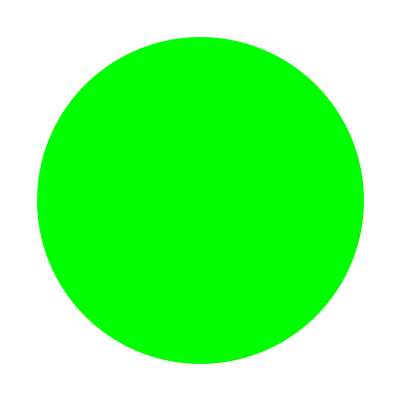

```mathematica
disk[{3,0},"color"->Green,"radius"->2]
```



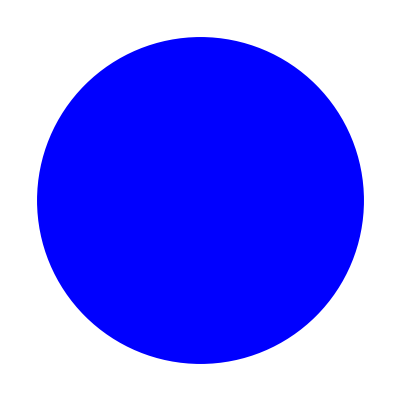

```mathematica
disk[{-2,-3}]
disk[{3,0},"color"->Blue]
```

## 6 Функциональное программирование

### Map

```mathematica
Map[f,{1,a,2,3,4,b}]
f/@{1,2,3,54,,e,f,g}
f[{1,a,2,3,4,b}]
SetAttributes[f,Listable]
f[{1,a,2,3,4,b}]
```

{f[1],f[a],f[2],f[3],f[4],f[b]}

{f[1],f[2],f[3],f[54],f[Null],f[e],f[f],f[g]}

{f[1],f[a],f[2],f[3],f[4],f[b]}

{f[1],f[a],f[2],f[3],f[4],f[b]}

```mathematica
f[x_,y_]:=Sin[x+y]
list=Range[5];
f[#,π]&/@list
```

{-Sin[1],-Sin[2],-Sin[3],-Sin[4],-Sin[5]}

#### Кумулятивные суммы

```mathematica
ы=0;
Map[(ы+=#)&,Range[10]]
```

{1,3,6,10,15,21,28,36,45,55}

#### MapIndexed

#### Применение не ко всему списку

```mathematica
testlist={1,2,3,5,3,-1,2,3,4,-5,5,6,7};
result={};
VectorQ[testlist,If[#≥0,AppendTo[result,√#];True]&]
result
```

False

{1,√2,√3,√5,√3}

#### Применение к уровням выражений

```mathematica
ClearAll[a,m,f]
a=Array[#1+#2&,{3,3}]
Map[f,a]
Map[f,a,{2}]
```

{{2,3,4},{3,4,5},{4,5,6}}

{f[{2,3,4}],f[{3,4,5}],f[{4,5,6}]}

{{f[2],f[3],f[4]},{f[3],f[4],f[5]},{f[4],f[5],f[6]}}

### MapAt

#### Применение функции ко всем четным элементам списка

```mathematica
ClearAll[f];
list=RandomInteger[{-5,5},20]
```

{-2,5,0,3,-5,2,-2,-3,-5,2,5,5,5,4,4,4,-5,0,0,-3}

```mathematica
MapAt[f,list,Position[list,_?EvenQ]]
```

{f[-2],5,f[0],3,-5,f[2],f[-2],-3,-5,f[2],5,5,5,f[4],f[4],f[4],-5,f[0],f[0],-3}

#### Порядок применения

```mathematica
g=expr@@Range[5]
n=1;
MapAt[f,g,{{1},{2},{3},{3},{2},{2},{4}}]
```

expr[1,2,3,4,5]

expr[f[1],f[f[f[2]]],f[f[3]],f[4],5]

```mathematica
MapAt[{#,n++}&,g,{{1},{2},{3},{3},{2},{2},{4}}]
(* индексы упорядочиваются в порядке обхода выражения в глубину*)
```

{{1,1},{{{2,2},3},4},{{3,5},6},{4,7},5}

### MapAll

```mathematica
{1,2,3,Sequence[],7,8,9}
```

{1,2,3,7,8,9}

### Scan

```mathematica
Scan[Print,Range[5]]
```

1

2

3

4

5

```mathematica
Map[Print,Range[5]]
```

1

2

3

4

5

{Null,Null,Null,Null,Null}

```mathematica
Total[Range[10]^2]
```

385

### MapIndexed

```mathematica
MapIndexed[Print[#2,": ",#1]&,Range[5]];
MapIndexed[Print[#2,": ",#1]&,a]
```

{1}: 1

{2}: 2

{3}: 3

{4}: 4

{5}: 5

{1}: {2,3,4}

{2}: {3,4,5}

{3}: {4,5,6}

```mathematica
MatrixForm[a]
MapIndexed[Print[#2,": ",#1]&,a,{2}]
```

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

{1,1}: 2

{1,2}: 3

{1,3}: 4

{2,1}: 3

{2,2}: 4

{2,3}: 5

{3,1}: 4

{3,2}: 5

{3,3}: 6

{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}

```mathematica
m=MapIndexed[x^Total[#2]&,IdentityMatrix[3],{2}]
```

{{x^2,x^3,x^4},{x^3,x^4,x^5},{x^4,x^5,x^6}}

```mathematica
Equal@@#2
```

False

### Apply

```mathematica
ClearAll[f,g,x]
Apply[f,g[x]]
Plus@@{1,2,3,4,5}
```

f[x]

15

#### Уровни

```mathematica
a=Array[RandomInteger[{-5,5}]&,{3,3}]
```

{{1,3,-2},{3,0,2},{3,-3,3}}

```mathematica
Apply[f,a]
```

f[{1,3,-2},{3,0,2},{3,-3,3}]

```mathematica
Apply[f,a,{1}]
f@@@a
```

{f[1,3,-2],f[3,0,2],f[3,-3,3]}

{f[1,3,-2],f[3,0,2],f[3,-3,3]}

#### Выделяем диагонали матрицы

```mathematica
Subtract
Flatten
Sort
Split
Map (Part)
```

#### Передача последовательности аргументов

### Thread

```mathematica
ClearAll[f,a]
f[Range[5]]
Thread[f[Range[5]]]
```

f[{1,2,3,4,5}]

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
list={{1,2},{a,b}};
```

```mathematica
Thread[f[{{1,2},{a,b}}]]
Thread[f[{1,2},{a,b}]]
```

{f[{1,2}],f[{a,b}]}

{f[1,a],f[2,b]}

```mathematica
Thread[f[{1,2,3,4},{a,b,c,d}]]
```

```mathematica
Thread[f[{1,2,3,4},{a,b,c}]]
```

```mathematica
Thread[f[{1,2,3,4},a]]
Thread[f[{1,2,3,4},a,b,c]]
{1,2,3,4}+a+b+c
```

{f[1,a],f[2,a],f[3,a],f[4,a]}

{f[1,a,b,c],f[2,a,b,c],f[3,a,b,c],f[4,a,b,c]}

{1+a+b+c,2+a+b+c,3+a+b+c,4+a+b+c}

### MapThread

```mathematica
MapThread[f,{{1,2,3,4},{a,b,c,d}}]
```

{f[1,a],f[2,b],f[3,c],f[4,d]}

```mathematica
MapThread[f,{1,2,3,4},1]
```

```mathematica
MapThread[f,{{1,11},{2,22},{3,33},{4,44}},1]
```

{f[1,2,3,4],f[11,22,33,44]}

```mathematica
MapThread[f,{{1,11},{2,22},{3,33},{4,44}},2]
```

MapThread::mptd: Object {1, 11} at position {2, 1} in MapThread[f, {{1, 11}, {2, 22}, {3, 33}, {4, 44}}, 2] has only 1 of required 2 dimensions.

MapThread[f,{{1,11},{2,22},{3,33},{4,44}},2]

```mathematica
MapThread[f,{{1,2,3,4},a}]
```

MapThread::mptd: Object a at position {2, 2} in MapThread[f, {{1, 2, 3, 4}, a}] has only 0 of required 1 dimensions.

MapThread[f,{{1,2,3,4},a}]

```mathematica
Trace[MapThread[Times,{Range[10],Range[11,20]}]]
```

{{{Range[10],{1,2,3,4,5,6,7,8,9,10}},{Range[11,20],{11,12,13,14,15,16,17,18,19,20}},{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20}}},MapThread[Times,{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20}}],{1 11,2 12,3 13,4 14,5 15,6 16,7 17,8 18,9 19,10 20},{1 11,11},{2 12,24},{3 13,39},{4 14,56},{5 15,75},{6 16,96},{7 17,119},{8 18,144},{9 19,171},{10 20,200},{11,24,39,56,75,96,119,144,171,200}}

```mathematica
Trace[Thread[Times[Range[10],Range[11,20]]]]
```

{{{Range[10],{1,2,3,4,5,6,7,8,9,10}},{Range[11,20],{11,12,13,14,15,16,17,18,19,20}},{1,2,3,4,5,6,7,8,9,10} {11,12,13,14,15,16,17,18,19,20},{11,24,39,56,75,96,119,144,171,200}},Thread[{11,24,39,56,75,96,119,144,171,200}],{11,24,39,56,75,96,119,144,171,200}}

```mathematica
Range[10]Range[11,20]
```

{11,24,39,56,75,96,119,144,171,200}

```mathematica
f[a_,b_,c_]:=2a+Sin[b c]
{Array[a,5],Array[b,5],Array[c,5]}
vars=Array[#,5]&/@{a,b,c}
```

{{a[1],a[2],a[3],a[4],a[5]},{b[1],b[2],b[3],b[4],b[5]},{c[1],c[2],c[3],c[4],c[5]}}

{{a[1],a[2],a[3],a[4],a[5]},{b[1],b[2],b[3],b[4],b[5]},{c[1],c[2],c[3],c[4],c[5]}}

```mathematica
MapThread[f,vars]
```

{2 a[1]+Sin[b[1] c[1]],2 a[2]+Sin[b[2] c[2]],2 a[3]+Sin[b[3] c[3]],2 a[4]+Sin[b[4] c[4]],2 a[5]+Sin[b[5] c[5]]}

```mathematica
Thread[f@@vars]
```

{2 a[1]+Sin[b[1] c[1]],2 a[2]+Sin[b[2] c[2]],2 a[3]+Sin[b[3] c[3]],2 a[4]+Sin[b[4] c[4]],2 a[5]+Sin[b[5] c[5]]}

```mathematica
f@@@Transpose[vars]
```

{2 a[1]+Sin[b[1] c[1]],2 a[2]+Sin[b[2] c[2]],2 a[3]+Sin[b[3] c[3]],2 a[4]+Sin[b[4] c[4]],2 a[5]+Sin[b[5] c[5]]}

### Inner

```mathematica
{1,2,3}.{a,b,c}
Inner[Times,{1,2,3},{a,b,c},Plus]
```

a+2 b+3 c

a+2 b+3 c

```mathematica
ClearAll[f,g,a,b,c]
Inner[f,{1,2,3},{a,b,c},g]
g@@Thread[f[{1,2,3},{a,b,c}]]
```

g[f[1,a],f[2,b],f[3,c]]

g[f[1,a],f[2,b],f[3,c]]

### Outer

{1,2,3,4,5}

{1,2,3}

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}},{{5,1},{5,2},{5,3}}}

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}},{{5,1},{5,2},{5,3}}}

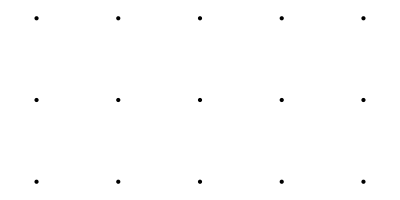

```mathematica
xnodes=Range[5]
ynodes=Range[3]
Table[{x,y},{x,xnodes},{y,ynodes}]
Outer[List,xnodes,ynodes]
Graphics@Point[Join@@%]
```

```mathematica
Flatten[Outer[List,{0,1},{0,1},{0,1},{0,1}],3]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

### Nest, NestList

```mathematica
Nest[f,x,5]
NestList[f,x,5]
```

f[f[f[f[f[x]]]]]

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

### NestWhile, NestWhileList

```mathematica
NestList[#^2&,.5,100]
NestWhileList[#^2&,.5,Abs[#]>0.01&]
```

General::unfl: Underflow occurred in computation.

{0.5,0.25,0.0625,0.00390625,0.0000152588,2.32831×10^-10,5.42101×10^-20,2.93874×10^-39,8.63617×10^-78,7.45834×10^-155,5.562684646268×10^-309,3.09434604738258×10^-617,9.57497746095219×10^-1234,9.1680193377742×10^-2467,8.4052578577802×10^-4933,7.0648359655776×10^-9865,4.991190722052×10^-19729,2.49119848239×10^-39457,6.206069878661×10^-78914,3.85153033388×10^-157827,1.48342859128×10^-315653,2.20056038543×10^-631306,4.84246600993×10^-1262612,2.3449477057×10^-2525223,5.4987797426×10^-5050446,3.0236578658×10^-10100891,9.142506889×10^-20201782,8.358543222×10^-40403563,6.98652448×10^-80807125,4.88115243×10^-161614249,Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[],Underflow[]}

{0.5,0.25,0.0625,0.00390625}

### Fold, FoldList

```mathematica
Fold[f,x,{1,2,3,4,5}]
```

```mathematica
FoldList[f,x,{a,b,c,d,e}]
```

f[f[f[f[f[x,1],2],3],4],5]

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c],f[f[f[f[x,a],b],c],d],f[f[f[f[f[x,a],b],c],d],e]}

```mathematica
list={4,-1,-2,0,4,5,3,2,6,7,5,3,2,8,4,2,9}
DeleteDuplicates[Rest[FoldList[Max,-∞,list]]]
```

{4,-1,-2,0,4,5,3,2,6,7,5,3,2,8,4,2,9}

{4,5,6,7,8,9}

### FixedPoint, FixedPointList

```mathematica
Clear[c];
c[n_?OddQ]:=3*n+1;
c[n_?EvenQ]:=n /2;

q=1000
NestWhileList[c,q,#≠1&]
```

1000

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Through

```mathematica
Through[{f,g,h}[x,y]]
```

{f[x,y],g[x,y],h[x,y]}

```mathematica
#[x,y]&/@{f,g,h}
```

{f[x,y],g[x,y],h[x,y]}

### Reap and Sow

```mathematica
data=RandomReal[{-5,5},{10,10}];
positive={};
positive
Scan[If[#>0,AppendTo[positive,#]]&,data,{2}];

r=Reap[Scan[If[#>0,Sow[#,"положительные"],Sow[#,"неотрицательные"]]&,data,{2}];Привет,___,#1->#2&]
r⟦2,1⟧
```

{}

{Привет,{положительные→{1.08974,4.54264,2.51537,4.04578,3.44382,0.375871,1.85591,2.1334,2.49486,0.349842,4.63484,2.90261,0.374359,4.07845,3.95617,3.75801,0.315808,4.63123,4.99979,4.06613,4.31578,0.523441,3.62093,3.67492,0.476697,4.37698,2.44678,3.85524,3.15731,4.07908,1.18532,4.99641,1.00314,4.15252,4.04914,3.16713,0.0160819,2.96161,2.034,2.10456,2.40368,3.03044,3.10609,1.1635,4.54122,0.755407,1.59128,3.99389,3.19988,4.86899,2.76379,2.19505,2.24333,1.30985,2.72916,1.15479,2.75046,2.31136},неотрицательные→{-0.178427,-0.183595,-4.96089,-0.0568967,-4.57437,-1.49097,-0.748606,-2.86509,-3.12522,-2.33116,-4.8008,-4.15017,-0.0796851,-3.1297,-2.51332,-0.801462,-1.33491,-0.660074,-2.97224,-4.741,-1.04073,-4.11982,-2.96914,-3.40635,-2.43965,-4.55086,-3.42081,-0.362115,-3.71553,-4.2693,-1.2308,-1.65005,-4.38115,-3.33436,-4.83036,-4.0164,-0.209883,-2.79752,-2.99841,-4.95647,-0.07197,-2.70561}}}

положительные→{1.08974,4.54264,2.51537,4.04578,3.44382,0.375871,1.85591,2.1334,2.49486,0.349842,4.63484,2.90261,0.374359,4.07845,3.95617,3.75801,0.315808,4.63123,4.99979,4.06613,4.31578,0.523441,3.62093,3.67492,0.476697,4.37698,2.44678,3.85524,3.15731,4.07908,1.18532,4.99641,1.00314,4.15252,4.04914,3.16713,0.0160819,2.96161,2.034,2.10456,2.40368,3.03044,3.10609,1.1635,4.54122,0.755407,1.59128,3.99389,3.19988,4.86899,2.76379,2.19505,2.24333,1.30985,2.72916,1.15479,2.75046,2.31136}

## 7 Интерактивные средства языка

```mathematica
a=0;x=0;
Dynamic[a++;x]
```

```mathematica
DynamicModule[{x=0},Button[Dynamic[x],x++]]
```

```mathematica
FullForm[]
```

DynamicModule[List[Set[x,15]],Button[Dynamic[x,Rule[ImageSizeCache,List[28.,List[0.,17.]]]],Increment[x],Rule[Appearance,Automatic],Rule[Evaluator,Automatic],Rule[Method,"Preemptive"]],RuleDelayed[DynamicModuleValues,List[]]]

```mathematica
FullForm[]
```

DynamicModule[List[Set[x,30]],Button[Dynamic[x,Rule[ImageSizeCache,List[28.,List[0.,17.]]]],Increment[x],Rule[Appearance,Automatic],Rule[Evaluator,Automatic],Rule[Method,"Preemptive"]],RuleDelayed[DynamicModuleValues,List[]]]

```mathematica
EventHandler[]
```

## 8 Средства повышения производительности

```mathematica
mandelComp=Compile[{{c,_Complex}},Module[{num=1},FixedPoint[(num++;#^2+c)&,0,99,SameTest->(Re[#]^2+Im[#]^2≥4&)];num],CompilationTarget->"WVM",RuntimeAttributes->{Listable},Parallelization->True];

data=ParallelTable[a+I b,{a,-.715,-.61,.01},{b,-.5,-.4,.01}];

Graphics[Raster[Rescale[mandelComp[data]],ColorFunction->"TemperatureMap"],ImageSize->400,PlotRangePadding->0]
```

-Graphics-

```mathematica
f=#^3-1&;
newton=Evaluate[#-f[#]/f'[#]//Simplify]&;
p=1.+I;
d=2.;
n=433;
step=2 d/n;
grid=Range[-d,d,step];
mesh=Outer[p+#1+I#2&,grid,grid];
```

```mathematica
nSteps[p_]:=Module[{cnt=0},
FixedPoint[(cnt++;newton[#])&,p,99];
cnt
];

nStepsComp=Compile[{{p,_Complex}}
,Module[{cnt=0},
FixedPoint[(cnt++;newton[#])&,p,50];
cnt
]
,RuntimeAttributes->{Listable}
,Parallelization->True
,CompilationOptions->{"InlineExternalDefinitions"->True}
];
```

```mathematica
SetAttributes[nSteps,{Listable}]
```

```mathematica
AbsoluteTiming[data=nSteps[mesh];]
```

{5.2212987,Null}

```mathematica
AbsoluteTiming[data=Map[nSteps,mesh,{2}];]
```

{5.2513003,Null}

```mathematica
AbsoluteTiming[data=Map[nStepsComp,mesh,{2}];]
```

{3.376193,Null}

```mathematica
AbsoluteTiming[data=ParallelMap[nSteps,mesh,{2}];]
```

{6.1313507,Null}

```mathematica
AbsoluteTiming[data=ParallelMap[nStepsComp,mesh,{2}];]
```

{0.5540316,Null}

```mathematica
(*!!!!!!!!!*)
AbsoluteTiming[data=nStepsComp[mesh];]
```

{0.7790445,Null}

```mathematica
data
```

```mathematica
Graphics[Raster[Rescale@data,ColorFunction->"TemperatureMap"]]
```

-Graphics-

```mathematica
nSteps[0.1]
```

16

```mathematica
ArrayPlot[data]
```

-Graphics-

CompiledFunction[{p},Module[{cnt=0},FixedPoint[(cnt++;newton[#1])&,p,99];cnt],-CompiledCode-]

CompiledFunction::cfsa: Argument {} at position 1 should be a "machine-size complex number".

1

```mathematica
DownValues[nSteps]
```

{HoldPattern[nSteps[p_]]:>Module[{cnt=0},FixedPoint[(cnt++;newton[#1])&,p,99];cnt]}

```mathematica
Max[data]
```

50